# Short-term Energy Forecast Using Neural Networks

Using a neural network to estimate energy use for the Boston metropolitan area for the next 24 hours trained with 11 months of actual data

Jaime Buitrago, Jun. 24,  2018

Short-term (24-hour) load forecasting is a very important topic in today’s energy infrastructure.  By estimating how much energy will be used on an hourly basis during the next day, utility operators plan the staging of power sources and maintenance operations.  This study presents an approach utilizing neural networks. Using actual energy use data for the Boston metropolitan area for a period of 11 months, a neural network was used to predict the next 24 hour period.

## Data Description

Energy is not used in a constant manner in industrial, commercial, and residential areas.  A typical day starts at midnight with very little energy use:  most industrial plants and commercial stores are closed, and residences use just enough power to drive their air conditioners or heaters, if necessary, and some street lighting is used.  As the day breaks, energy use increases rapidly, when people are getting ready to go to work and school.  By noon time, energy use is very high, and typically by 3 pm it is at its peak.  Then the afternoon brings other uses, such as more lighting and heating during the winter, and the evening shows a steady consumption.  The night reduces the use to a minimum.

```mathematica
load24={1395.1630859,1387.2364502,1446.8320313,1702.9815674,1770.1772461,1793.1159668,1820.2614746,1859.3359375,1932.8875732,1920.3845215,1865.84729,1935.8175049,2056.265625,2082.7646484,2247.3081055,2263.6113281,2228.5449219,2148.3798828,2051.1557617,1924.90271,1790.951416,1883.3079834,1728.7506104,1611.3856201}
```

{1395.16,1387.24,1446.83,1702.98,1770.18,1793.12,1820.26,1859.34,1932.89,1920.38,1865.85,1935.82,2056.27,2082.76,2247.31,2263.61,2228.54,2148.38,2051.16,1924.9,1790.95,1883.31,1728.75,1611.39}

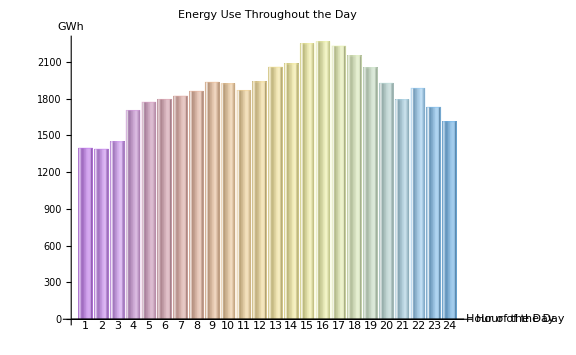

```mathematica
BarChart[load24,ChartLabels->Range[24],ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel", ImageSize->Large,PlotRange->All,AxesLabel->{"Hour of the Day","GWh" } , PlotLabel->"Energy Use Throughout the Day",AxesOrigin-> Automatic]
```

## Section Header

Or show an example of application ...

Another way to start an exposition, or to expand on the basics, is to provide an example showing the application of the topic. The example might be something you arrive at by the end of the exposition, repeating that conclusion here is acceptable if it's reasonably self-contained. It might also be an example a problem scenario and the exposition explains a solution.

Always have code text as a lead-in to code that follows, to concisely indicate what it does:

```mathematica
Code (* demonstrate a specific application *)
```

## Section Header

Add more sections as needed to explain the topic....

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins

derivation

applications

common misunderstandings

recent developments

unanswered questions

## Further explorations

Name of a related topic for exploration

Name of another related topic for exploration (repeat as needed)

## Author contact information

emailaddress@author.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)